## §1 毕达哥拉斯定理

满足a^2+b^2==c^2 的(a,b,c)称为毕达哥拉斯三元数.

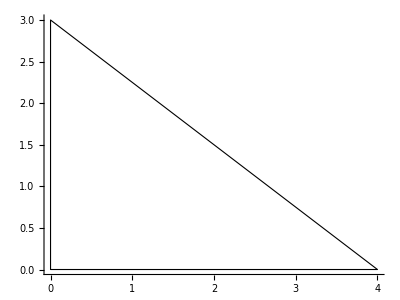

```mathematica
Graphics[{EdgeForm[Black],White,Triangle[{{0,0},{0,3},{4,0}}]},Axes->True]
```

生成毕达哥拉斯三元数的一般公式是
a=(p^2-q^2)r,b=2p q r,c=(p^2+q^2)r

```mathematica
(*习题1~3*)
a={119,3367,4601,12709,65,319,2291,799,481,4961,45,1679,161,1771,56};
c={169,4825,6649,18541,97,481,3541,1249,769,8161,75,2929,289,3229,106};
b=√(c^2-a^2)
Print["In list b which can't be divised by 60 are ",Select[b,Divisible[#,60]==False&]]
Print["In list b which can't be divised by 30 are ",Select[b,Divisible[#,30]==False&]]
Print["In list b which can't be divised by 12 are ",Select[b,Divisible[#,12]==False&]]
Print[Mod[1^2,4]," ",Mod[2^2,4]," ",Mod[3^2,4]]
Clear["Global`*"]
```

{120,3456,4800,13500,72,360,2700,960,600,6480,60,2400,240,2700,90}

In list b which can't be divised by 60 are {3456,72,90}

In list b which can't be divised by 30 are {3456,72}

In list b which can't be divised by 12 are {90}

1 0 1

(*习题4*)
如果a, b同时为奇数, 则c为偶数.又由于c为偶数, 且c为完全平方数, 则c可以被4整除.但奇数的平方Mod4仅余1, 两奇数平方之和Mod4余2;故毕达哥拉斯三元数(a,b,c)中a,b不能同时为奇数.